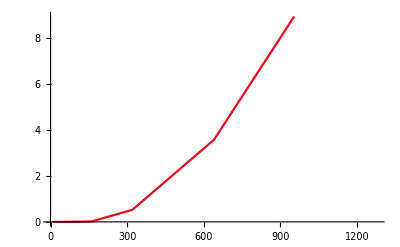
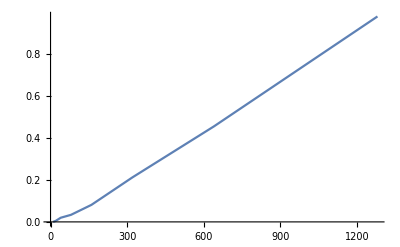
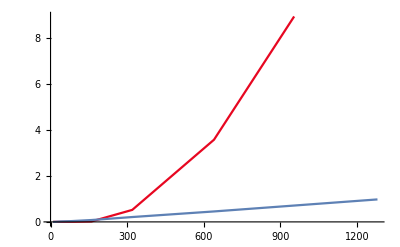
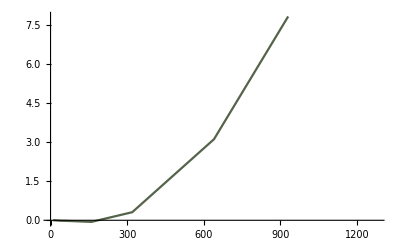

```mathematica
list1=Import["E:\\study_materials\\Finite Element Method\\Program\\Program5\\code\\cg.txt","Table"];
list2=Import["E:\\study_materials\\Finite Element Method\\Program\\Program5\\code\\MG.txt","Table"];
list=Table[{list1[[i,1]],list1[[i,2]]-list2[[i,2]]},{i,Length[list1]}];
img1=ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]];
img2=ListLinePlot[list2];
{img1,img2,Show[img1,img2,Range->All],ListLinePlot[list,PlotStyle->ColorData[4,"ColorList"]]}
```

```mathematica
(*求收敛阶*)
list2=Import["E:\\study_materials\\Finite Element Method\\Program\\Program5\\code\\mg.txt","Table"];
error=Table[{0,0,0},{i,Length[list2]}];
error[[1]]={list2[[1,1]],list2[[1,2]],"——"};
For[l=2,l≤Length[list2],l++,
error[[l]]={list2[[l,1]],list2[[l,2]],Log[list2[[l,2]]/list2[[l-1,2]]]/Log[2]};
];
PrependTo[error,{"n","time","Order"}];
GridBox[error,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

```mathematica
(*MG的时间增长求收敛阶*)
list2=Import["E:\\study_materials\\Finite Element Method\\Program\\Program5\\code\\cg.txt","Table"];
error=Table[{0,0,0},{i,Length[list2]}];
error[[1]]={list2[[1,1]],list2[[1,2]],"——"};
For[l=2,l≤Length[list2],l++,
error[[l]]={list2[[l,1]],list2[[l,2]],Log[list2[[l,2]]/list2[[l-1,2]]]/Log[2]};
];
PrependTo[error,{"n","time","Order"}];
GridBox[error,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

n | time | Order
10 | 0.0000685 | ——
20 | 0.0002613 | 1.93153
40 | 0.0009473 | 1.85811
80 | 0.0041658 | 2.1367
160 | 0.0186176 | 2.16
320 | 0.521905 | 2.00377
640 | 3.57052 | 2.00177
1280 | 14.492 | 2.02105

```mathematica
(*将N取大一些的时间增长阶*)
list2=Import["E:\\study_materials\\Finite Element Method\\Program\\Program5\\code\\mg.txt","Table"];
error=Table[{0,0,0},{i,Length[list2]}];
error[[1]]={list2[[1,1]],list2[[1,2]],"——"};
For[l=2,l≤Length[list2],l++,
error[[l]]={list2[[l,1]],list2[[l,2]],Log[list2[[l,2]]/list2[[l-1,2]]]/Log[2]};
];
PrependTo[error,{"n","time","Order"}];
GridBox[error,ColumnAlignments->Left,GridBoxDividers->{"Rows"->{{True}},"Columns"->{{True}}}]//DisplayForm
```

n | time | Order
10 | 0.0000758 | ——
20 | 0.0082819 | 6.77162
40 | 0.0140818 | 0.765798
80 | 0.0556167 | 1.98169
160 | 0.205971 | 1.88885
320 | 0.324359 | 0.65515
640 | 0.650401 | 1.00374
1280 | 1.25271 | 0.945651
2560 | 2.67802 | 1.09612
5120 | 5.37822 | 1.00596